# Migdal rate for inelastic dark matter

This notebook contains the calculations, analysis and figures for the paper here: https://arxiv.org/abs/2103.05890

## Introduction

- Gray (initialization) cells can be evaluated automatically
- Red cells are the main computations and can take minutes to run
- Blue cells create plots
- Purple cells create output files

## Constants

Fundamental constants:

```mathematica
amu=0.9314943 GeV;
mn=1.008665amu;
mp=1.007276amu;
ℏc=.19732698 GeV fm;
Centimeter= 1/ℏc 10^13 fm;
ℏ=(4.135667 10^-15 eV s)/(2π);
Me=511keV;
c=2.998 10^5 km/s;
GeVperKg=c^2((1000m)/km)^2(1J)/(1kg m^2/s^2)(1eV)/(1.602 10^-19 J)(1GeV)/(10^9 eV);
```

DM astrophysical parameters:

```mathematica
ρ=0.3GeV/cm^3;
v0=220km/s;
vesc=544km/s;
ve=240km/s;
VMAX=(vesc+ve)/c;
```

Reduced mass definition:

```mathematica
μ[x_,y_]:=(x y)/(x+y)
```

#### Set plot styles and custom plot functions

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,16,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];

topLeft[x_] := Placed[x, {Scaled[{.38, .95}], {.9, 1}}];
topRight[x_] := Placed[x,{Scaled[{.95, .95}], {.9, 1}}];
Legend//Clear;
Legend[legendList_,opt:OptionsPattern[{Position->"Right",Type->"Line",LineLegend}]] := Module[{f},
If[OptionValue[Type]=="Line",
f=LineLegend;];
If[OptionValue[Type]=="Swatch",
f=SwatchLegend;];
If[OptionValue[Position]=="Right",
   f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topRight//Return];
If[OptionValue[Position]=="Left",
   f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topLeft//Return];

f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//Placed[#,OptionValue[Position]]&//Return;
];

LogTicks//Clear;
LogTicks[min_,max_,step_] := Block[{lmin, lmax, t},
   lmin = Floor[Log10[min]];
   lmax = Floor[Log10[max]];
   t=0;
   Return[{Join[
      Table[{10^i, If[Mod[++t,step]==0,Superscript[10, i],Null], {0.012, 0}}, {i, Floor[lmin], Ceiling[lmax]}], (Flatten[#1, 1] &)[
       Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], 
        Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]], 
     Join[Table[{10^i, Null, {0.012, 0}}, {i, Floor[lmin], 
     Ceiling[lmax]}], (Flatten[#1, 1] &)[ Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]]}  ]
];
LogTicks[min_, max_] := LogTicks[min,max,1];
```

## Inelastic Kinematics

Energy conservation in the CoM frame gives: 
1/2 μ_i v_i^2=E_1'+E_2'+E_EM+δ_DM
1/2 μ_i v_i^2=p_F^2/(2 μ_F)+E_EM+δ_DM
p_F^2 = μ_i μ_F v_i^2-2 μ_F (E_EM+δ_DM) 

q^2=(p_F-p_i)^2
Momentum transfer is same in both frames:
E_R≃ (p_F^2+p_i^2-2 p_F p_i cosθ_CM)/(2 m_T)

```mathematica
Er==1/(2 mT)(μT μTf vi^2-2μTf (δEM+δDM)+μT^2 vi^2-2 √(μT μTf vi^2-2μTf (δEM+δDM))μT vi cosθCM)/.{μT->(mx mT)/(mx+mT), μTf->((mx+δDM) mT)/((mx+δDM)+mT)}//Simplify
```

Er==(mT mx (mT+mx) vi^2 (mx+δDM)+mT mx^2 vi^2 (mT+mx+δDM)-2 (mT+mx)^2 (mx+δDM) (δDM+δEM)-2 cosθCM mx (mT+mx) vi (mT+mx+δDM) √((mT (mx+δDM) (mT mx vi^2-2 mT (δDM+δEM)-2 mx (δDM+δEM)))/((mT+mx) (mT+mx+δDM))))/(2 (mT+mx)^2 (mT+mx+δDM))

Define limits of recoil energy (cosθCM = ±1):

```mathematica
ErMin[vi_?NumericQ,δDM_?NumericQ,δEM_?NumericQ,mx_?NumericQ,mT_?NumericQ]:=1/(2 (mT+mx)^2 (mT+mx+δDM))(mT mx (mT+mx) vi^2 (mx+δDM)+mT mx^2 vi^2 (mT+mx+δDM)-2 (mT+mx)^2 (mx+δDM) (δDM+δEM)-2 mx (mT+mx) vi (mT+mx+δDM) √((mT (mx+δDM) (mT mx vi^2-2 mT (δDM+δEM)-2 mx (δDM+δEM)))/((mT+mx) (mT+mx+δDM))));
ErMax[vi_?NumericQ,δDM_?NumericQ,δEM_?NumericQ,mx_?NumericQ,mT_?NumericQ]:=1/(2 (mT+mx)^2 (mT+mx+δDM))(mT mx (mT+mx) vi^2 (mx+δDM)+mT mx^2 vi^2 (mT+mx+δDM)-2 (mT+mx)^2 (mx+δDM) (δDM+δEM)+2 mx (mT+mx) vi (mT+mx+δDM) √((mT (mx+δDM) (mT mx vi^2-2 mT (δDM+δEM)-2 mx (δDM+δEM)))/((mT+mx) (mT+mx+δDM))));
```

Global max inelastic energy:

```mathematica
δMaxGeV[mX_,mT_]= (μ[mT,mX] VMAX^2)/2;
```

Maximum inelastic energy for a given nuclear recoil:

```mathematica
EemMaxERGeV[ER_,Vmax_,mX_,mT_]=√(2mT ER Vmax^2)-ER (mT+mX)/mX;
```

Define integration limits:

```mathematica
(ErMIN==1/(2 (mT+mx)^2 (mT+mx+δDM))(mT mx (mT+mx) vi^2 (mx+δDM)+mT mx^2 vi^2 (mT+mx+δDM)-2 (mT+mx)^2 (mx+δDM) (δDM+δEM)-2 mx (mT+mx) vi (mT+mx+δDM) √((mT (mx+δDM) (mT mx vi^2-2 mT (δDM+δEM)-2 mx (δDM+δEM)))/((mT+mx) (mT+mx+δDM))))/.δEM->Edet-LXe ErMIN)//Solve[#,ErMIN]&//FullSimplify
```

{{ErMIN→(mT^3 (2 mx^2 vi^2+mx (-2+vi^2) δDM-2 δDM^2)-2 Edet (mT+mx)^2 (mx+δDM) (mT-(-1+LXe) (mx+δDM))+2 mT mx ((mx+δDM) (mx^2 vi^2+mx (-3+2 LXe+vi^2) δDM+2 (-1+LXe) δDM^2)-2 √(1/(mT+mx)^4 mT mx^2 vi^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LXe mx)+mT mx vi^2)+(-2 (mT+mx)^2 (Edet-Edet LXe+mT+mx-LXe mx)+mT mx (mT-LXe mT+mx) vi^2) δDM+2 (-1+LXe) (mT+mx)^2 δDM^2)))+mT^2 ((mx+δDM) (4 mx^2 vi^2+mx (-6+2 LXe+vi^2-LXe vi^2) δDM+2 (-1+LXe) δDM^2)-2 √(1/(mT+mx)^4 mT mx^2 vi^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LXe mx)+mT mx vi^2)+(-2 (mT+mx)^2 (Edet-Edet LXe+mT+mx-LXe mx)+mT mx (mT-LXe mT+mx) vi^2) δDM+2 (-1+LXe) (mT+mx)^2 δDM^2)))+2 mx^2 ((-1+LXe) δDM (mx+δDM)^2-√(1/(mT+mx)^4 mT mx^2 vi^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LXe mx)+mT mx vi^2)+(-2 (mT+mx)^2 (Edet-Edet LXe+mT+mx-LXe mx)+mT mx (mT-LXe mT+mx) vi^2) δDM+2 (-1+LXe) (mT+mx)^2 δDM^2))))/(2 (mT+mx)^2 (mT-(-1+LXe) (mx+δDM))^2)},{ErMIN→(mT^3 (2 mx^2 vi^2+mx (-2+vi^2) δDM-2 δDM^2)-2 Edet (mT+mx)^2 (mx+δDM) (mT-(-1+LXe) (mx+δDM))+2 mx^2 ((-1+LXe) δDM (mx+δDM)^2+√(1/(mT+mx)^4 mT mx^2 vi^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LXe mx)+mT mx vi^2)+(-2 (mT+mx)^2 (Edet-Edet LXe+mT+mx-LXe mx)+mT mx (mT-LXe mT+mx) vi^2) δDM+2 (-1+LXe) (mT+mx)^2 δDM^2)))+2 mT mx ((mx+δDM) (mx^2 vi^2+mx (-3+2 LXe+vi^2) δDM+2 (-1+LXe) δDM^2)+2 √(1/(mT+mx)^4 mT mx^2 vi^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LXe mx)+mT mx vi^2)+(-2 (mT+mx)^2 (Edet-Edet LXe+mT+mx-LXe mx)+mT mx (mT-LXe mT+mx) vi^2) δDM+2 (-1+LXe) (mT+mx)^2 δDM^2)))+mT^2 ((mx+δDM) (4 mx^2 vi^2+mx (-6+2 LXe+vi^2-LXe vi^2) δDM+2 (-1+LXe) δDM^2)+2 √(1/(mT+mx)^4 mT mx^2 vi^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LXe mx)+mT mx vi^2)+(-2 (mT+mx)^2 (Edet-Edet LXe+mT+mx-LXe mx)+mT mx (mT-LXe mT+mx) vi^2) δDM+2 (-1+LXe) (mT+mx)^2 δDM^2))))/(2 (mT+mx)^2 (mT-(-1+LXe) (mx+δDM))^2)}}

```mathematica
%/.{δDM->0,Edet->10^-6,mT->120,mx->4,vi->VMAX,LXe->.15}
```

{{ErMIN→6.33325×10^-10},{ErMIN→1.65906×10^-6}}

```mathematica
{ErMinGeV[(δDM) 10^-6,Edet,mx,131. amu/GeV] 10^6,ErMaxGeV[(δDM) 10^-6,Edet,mx,131. amu/GeV] 10^6}/.{δDM->0,Edet->0,mx->1,vi->VMAX}
```

{7.77331×10^-18,0.11054}

```mathematica
ErMinGeV[δDM_?NumericQ,Edet_?NumericQ,mx_?NumericQ,mT_?NumericQ]:=(mT^3 (2 mx^2 VMAX^2+mx (-2+VMAX^2) δDM-2 δDM^2)-2 Edet (mT+mx)^2 (mx+δDM) (mT-(-1+LeffXe) (mx+δDM))+2 mT mx ((mx+δDM) (mx^2 VMAX^2+mx (-3+2 LeffXe+VMAX^2) δDM+2 (-1+LeffXe) δDM^2)-2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LeffXe mx)+mT mx VMAX^2)+(-2 (mT+mx)^2 (Edet-Edet LeffXe+mT+mx-LeffXe mx)+mT mx (mT-LeffXe mT+mx) VMAX^2) δDM+2 (-1+LeffXe) (mT+mx)^2 δDM^2)))+mT^2 ((mx+δDM) (4 mx^2 VMAX^2+mx (-6+2 LeffXe+VMAX^2-LeffXe VMAX^2) δDM+2 (-1+LeffXe) δDM^2)-2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LeffXe mx)+mT mx VMAX^2)+(-2 (mT+mx)^2 (Edet-Edet LeffXe+mT+mx-LeffXe mx)+mT mx (mT-LeffXe mT+mx) VMAX^2) δDM+2 (-1+LeffXe) (mT+mx)^2 δDM^2)))+2 mx^2 ((-1+LeffXe) δDM (mx+δDM)^2-√(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LeffXe mx)+mT mx VMAX^2)+(-2 (mT+mx)^2 (Edet-Edet LeffXe+mT+mx-LeffXe mx)+mT mx (mT-LeffXe mT+mx) VMAX^2) δDM+2 (-1+LeffXe) (mT+mx)^2 δDM^2))))/(2 (mT+mx)^2 (mT-(-1+LeffXe) (mx+δDM))^2)//
```

```mathematica
ErMaxGeV[δDM_?NumericQ,Edet_?NumericQ,mx_?NumericQ,mT_?NumericQ]:=(mT^3 (2 mx^2 VMAX^2+mx (-2+VMAX^2) δDM-2 δDM^2)-2 Edet (mT+mx)^2 (mx+δDM) (mT-(-1+LeffXe) (mx+δDM))+2 mx^2 ((-1+LeffXe) δDM (mx+δDM)^2+√(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LeffXe mx)+mT mx VMAX^2)+(-2 (mT+mx)^2 (Edet-Edet LeffXe+mT+mx-LeffXe mx)+mT mx (mT-LeffXe mT+mx) VMAX^2) δDM+2 (-1+LeffXe) (mT+mx)^2 δDM^2)))+2 mT mx ((mx+δDM) (mx^2 VMAX^2+mx (-3+2 LeffXe+VMAX^2) δDM+2 (-1+LeffXe) δDM^2)+2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LeffXe mx)+mT mx VMAX^2)+(-2 (mT+mx)^2 (Edet-Edet LeffXe+mT+mx-LeffXe mx)+mT mx (mT-LeffXe mT+mx) VMAX^2) δDM+2 (-1+LeffXe) (mT+mx)^2 δDM^2)))+mT^2 ((mx+δDM) (4 mx^2 VMAX^2+mx (-6+2 LeffXe+VMAX^2-LeffXe VMAX^2) δDM+2 (-1+LeffXe) δDM^2)+2 √(1/(mT+mx)^4 mT mx^2 VMAX^2 (mx+δDM) (mT+mx+δDM)^2 ((mT+mx)^2 (-2 Edet (mT+mx-LeffXe mx)+mT mx VMAX^2)+(-2 (mT+mx)^2 (Edet-Edet LeffXe+mT+mx-LeffXe mx)+mT mx (mT-LeffXe mT+mx) VMAX^2) δDM+2 (-1+LeffXe) (mT+mx)^2 δDM^2))))/(2 (mT+mx)^2 (mT-(-1+LeffXe) (mx+δDM))^2)
```

```mathematica
EdetMax[δDM_?NumericQ,mx_?NumericQ,mT_?NumericQ]:=-(-mT mx (mT+mx)^2 VMAX^2+2 (mT+mx)^2 (mT+mx-LeffXe mx) δDM-mT mx (mT-LeffXe mT+mx) VMAX^2 δDM-2 (-1+LeffXe) (mT+mx)^2 δDM^2)/(2 (mT+mx)^2 (mT-(-1+LeffXe) (mx+δDM)))
```

### Find v_min

Solving the simple case of δ_DM=0 gives the familiar result:

```mathematica
Solve[{Er==1/(2 mT)(μi μf vi^2-2μf (δEM+δDM)+μi^2 vi^2-2 √(μi μf vi^2-2μf (δEM+δDM))μi vi cosθCM)/.{cosθCM->-1, μf->μi,δDM->0}},vi]
```

{{vi→-(Er mT+δEM μi)/(√2 √Er √mT μi)},{vi→(Er mT+δEM μi)/(√2 √Er √mT μi)}}

```mathematica
VminApprox[ER_,δDM_,δEM_,mx_,mT_]=Abs[(ER mT+(δDM+δEM) μ[mx,mT])/(√2 √ER √mT μ[mx,mT])];
```

```mathematica
Solve[ER==1/(2 mT)(μi μf vi^2-2μf (δEM+δDM)+μi^2 vi^2-2 √(μi μf vi^2-2μf (δEM+δDM))μi vi cosθCM)/.{cosθCM->-1,μi->(mT mx)/(mT+mx),μf->(mT (mx+δDM))/(mT+(mx+δDM))},vi][[2]]//Simplify
```

{vi→√2 √(1/(mT^4 mx^2 δDM^2)(ER mT mx (mT+mx)^2 (2 mx (mx+δDM)^2+mT^2 (2 mx+δDM)+mT (4 mx^2+5 mx δDM+δDM^2))+mT^4 mx δDM (mx+δDM) (δDM+δEM)+2 mT^3 mx^2 δDM (mx+δDM) (δDM+δEM)+mT^2 mx^3 δDM (mx+δDM) (δDM+δEM)-2 √(ER mT^2 mx^3 (mT+mx)^4 (mx+δDM) (mT+mx+δDM)^2 (ER (mT+mx) (mT+mx+δDM)+mT δDM (δDM+δEM)))))}

```mathematica
VminBad[ER_,δDM_,δEM_,mx_,mT_]=√2 √(1/(mT^4 mx^2 δDM^2)(ER mT mx (mT+mx)^2 (2 mx (mx+δDM)^2+mT^2 (2 mx+δDM)+mT (4 mx^2+5 mx δDM+δDM^2))+mT^4 mx δDM (mx+δDM) (δDM+δEM)+2 mT^3 mx^2 δDM (mx+δDM) (δDM+δEM)+mT^2 mx^3 δDM (mx+δDM) (δDM+δEM)-2 √(ER mT^2 mx^3 (mT+mx)^4 (mx+δDM) (mT+mx+δDM)^2 (ER (mT+mx) (mT+mx+δDM)+mT δDM (δDM+δEM)))));
```

This formula has a pole at δ_DM->0, and exhibits stability issues at very particular values, improve stability with some redefinitions:

```mathematica
(Solve[0== μi(1+R) vi^2+2 √(μi μf vi^2-2μf (δEM+δDM)) vi+kk,vi]//FullSimplify)[[2]]/.{kk->-(2mT Er)/μi-2(δEM+δDM),R->μf/μi}/.{μi->(mT mx)/(mT+mx),μf->(mT (mx+δDM))/(mT+(mx+δDM))}//FullSimplify
```

{vi→2 √(-(Er (mT+mx)+mx (δDM+δEM))^2/(mx^2 (-4 √((Er mT^2 (mx+δDM) (Er (mT+mx) (mT+mx+δDM)-mT δDM (δDM+δEM)))/(mx (mT+mx+δDM)^2))-(2 mT (Er (mT+mx) (2 mx (mx+δDM)+mT (2 mx+δDM))-mT mx δDM (δDM+δEM)))/(mx (mT+mx) (mT+mx+δDM)))))}

```mathematica
Vmin[Er_,δDM_,δEM_,mx_,mT_]=(√2 mT (Er (mT+mx)+mx (δDM+δEM))//Abs)/((mT+mx) √((mT mx (Er mT ((mT mx)/(mT+mx)+(mT (mx+δDM))/(mT+mx+δDM))-(mT^3 mx δDM (δDM+δEM))/((mT+mx)^2 (mT+mx+δDM))+2 √((Er mT^4 mx (mx+δDM) (Er (mT+mx) (mT+mx+δDM)-mT δDM (δDM+δEM)))/((mT+mx)^2 (mT+mx+δDM)^2))))/(mT+mx)));
```

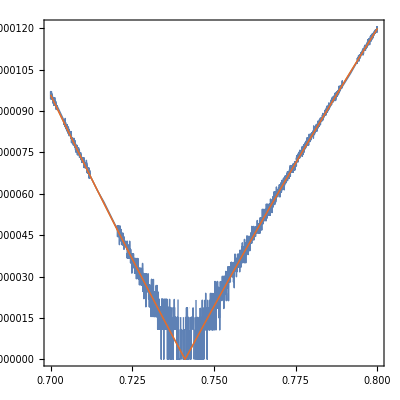

```mathematica
Plot[{VminBad[0.023918853046650618 10^-6,-4 10^-6,3.803008654588058*^-8,mx,131 amu/GeV],,Vmin[0.023918853046650618 10^-6,-4 10^-6,3.803008654588058*^-8,mx,131 amu/GeV],VminApprox[0.023918853046650618 10^-6,-4 10^-6,3.803008654588058*^-8,mx,131 amu/GeV]},{mx,.7,.8}]
```

The fractional difference between approximate formula and full formula are small in our region of interest, but start to become ~0.5% when we consider δDM/m_x~0.01:

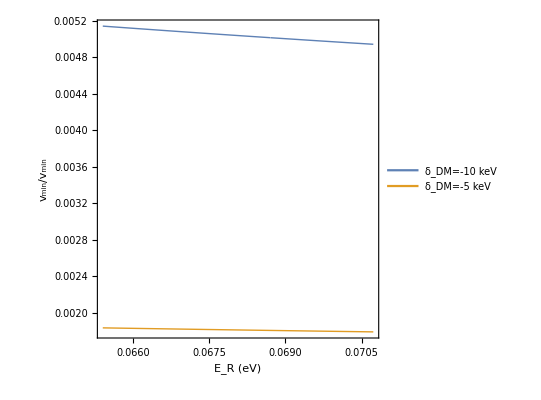

```mathematica
Plot[{(Vmin[ER 10^-9,-10^-5,10^-6,.001,131]-VminApprox[ER 10^-9,-10^-5,10^-6,.001,131])/Vmin[ER 10^-9,-10^-5,10^-6,.001,131],(Vmin[ER 10^-9,-5 10^-6,10^-6,.001,131]-VminApprox[ER 10^-9,-5 10^-6,10^-6,.001,131])/Vmin[ER 10^-9,-5 10^-6,10^-6,.001,131]},
{ER,ErMinGeV[-10^-5,10^-6,.001,131] 10^9,ErMaxGeV[-10^-5,10^-6,.001,131] 10^9},
FrameLabel->{"E_R (eV)","v_min/v_min"},PlotLegends->Legend[{"δ_DM=-10 keV","δ_DM=-5 keV"}]]
```

### Min recoil energy

mean collision time:

```mathematica
((.001 km)/(π (2 10^-10)^2(2860000/131 6.02 10^23))/(√((3 170Kelvin 8.6 10^-5 eV/Kelvin)/(131mn 10^9 eV/GeV))c))
```

3.38213×10^-12 s

Interatomic spacing:

```mathematica
d=((2860kg)/meter^3(6.02 10^23)/kg)^(-1/3)//Refine[#,Assumptions->meter>0]&
```

8.34345×10^-10 meter

Time to cross d using sound speed at 170K:

```mathematica
t1=d/vs/.vs->626 meter/s
```

1.33282×10^-12 s

This time-scale is on the conservative side of mean collision time.

Debye frequency (at 170K) - not defined for liquid - but for comparison:

```mathematica
ωDinv=1/((6 π^2 nXe soundSpeed^3)^(1/3)/.{nXe->((2.86 100^3)/meter^3(6.02 10^23)/131),soundSpeed->626 meter/s}//Refine[#,Assumptions->s>0]&)
```

1.73665×10^-13 s

Which has energy:

```mathematica
ωD ℏ
```

6.58212×10^-16 eV s ωD

So the impulse approximation requires time scale be faster than ~10^-12

```mathematica
MinERcutoffGeV=(100ℏ)/t1 (10^-9(*GeV*))/eV
```

4.93849×10^-11

Find conservative lower limit on mass:

```mathematica
NSolve[ErMaxGeV[(0) 10^-6,0,mx,131 amu/GeV]==MinERcutoffGeV,mx]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{mx→0.0209942}}

```mathematica
NSolve[ErMaxGeV[(10) 10^-6,0,mx,131 amu/GeV]==MinERcutoffGeV,mx]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{mx→0.365626}}

```mathematica
NSolve[ErMaxGeV[(-10) 10^-6,0,mx,131 amu/GeV]==MinERcutoffGeV,mx]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{mx→0.000595534}}

## Nuclear recoil rate

### Form factor

Define the Helm form factor:

```mathematica
F[A_,ErkeV_]:=3(Sin[q r]-(q r)Cos[q r])/(q r)^3 Exp[(-(q s)^2)/2]/.{q->6.92*10^-3 √A √ErkeV,r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9};
```

### Maxwell Boltzmann with cutoff

```mathematica
fMBc[v_,cosθ_,norm_]:=1/norm( Exp[-(v^2-2 ve/c v cosθ+(ve/c)^2)/(v0/c)^2]-Exp[-vesc^2/v0^2])HeavisideTheta[(vesc/c)^2-(v^2-2 ve/c v cosθ+(ve/c)^2)];
```

```mathematica
normMB=NIntegrate[fMBc[v ,cosθ,1]2π v^2,{v,0,(ve+vesc)/c},{cosθ,-1,1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Find speed distribution by integrating over the angles, with work-around for the step function (which mathematica does not integrate properly):

```mathematica
Fc//Clear;Fc[V_?NumericQ]=Piecewise[{{Integrate[fMBc[V,cosθ,normMB]2π V^2,{cosθ,-1,1},Assumptions->V∈Reals],V<(vesc-ve)/c},{0,V≥(vesc+ve)/c}},Integrate[fMBc[V,cosθ,normMB]2π V^2,{cosθ,1-((vesc/c)^2-(V-ve/c)^2)/(2 ve/c V),1},Assumptions->V∈Reals]];
```

```mathematica
normMB =π^(3/2)(v0/c)^3(Erf[vesc/v0]-4/(√π)Exp[-(vesc/v0)^2](vesc/(2 v0)+1/3(vesc/v0)^3));
```

```mathematica
fOnvMB[vmin_?NumericQ,V0_?NumericQ,Vesc_?NumericQ,Ve_?NumericQ]=
Piecewise[
{
{(π^(3/2)(V0)^2)/(2 normMB Ve/V0)(Erf[vmin/V0+Ve/V0]-Erf[vmin/V0-Ve/V0]-(4Ve)/(√π V0)Exp[-(Vesc/V0)^2](1+(Vesc/V0)^2-Ve^2/(3 V0^2)- (vmin/V0)^2)),
Ve/V0+vmin/V0<Vesc/V0},
{(π^(3/2)(V0)^2)/(2 normMB Ve/V0)(Erf[Vesc/V0]+Erf[-vmin/V0+Ve/V0]-2/(√π)Exp[-(Vesc/V0)^2]((Vesc/V0)+Ve/V0-(vmin/V0)-1/3(Ve/V0 -2(Vesc/V0) -(vmin/V0))((Vesc/V0)+Ve/V0-(vmin/V0))^2) ),vmin/V0>Abs[-Ve/V0+Vesc/V0] && (Ve/V0+Vesc/V0> vmin/V0)},
{Return[1/Ve],Ve/V0>vmin/V0+Vesc/V0},
{Return[0],Ve/V0+Vesc/V0<vmin/V0}
}
];
```

Numerical evaluation:

```mathematica
integrand[v_?NumericQ]:=Fc[v]/v;
```

```mathematica
G=ParallelTable[{vmin,NIntegrate[integrand[V],{V,vmin,(ve+vesc)/c}]},{vmin,0,(ve+vesc)/c,(ve+vesc)/(200c)}]//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
Gv[vmin_]:=If[vmin<VMAX,G[vmin],0];
```

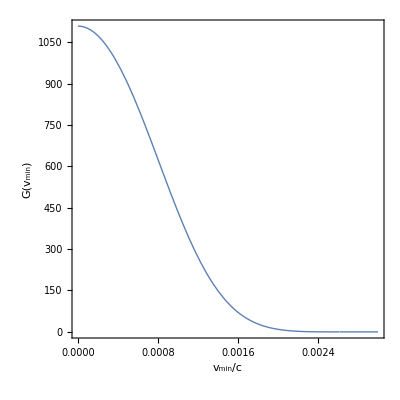

```mathematica
Plot[Gv[v],{v,0,.003}, FrameLabel->{"v_min/c","G(v_min)"}]
```

### Differential rates

Define rate in /tonne/yr/keV

```mathematica
dRdEr[ErkeV_?NumericQ,δDMkeV_?NumericQ,δEMkeV_?NumericQ,σncm2_?NumericQ,mxGeV_?NumericQ,A_?NumericQ]:=
(365.25 3600*24 s/(1(*year*)))(c(100000cm)/km)((1 GeV)/(10^6(*keV*)))(GeVperKg (1000kg)/(1(*tonne*)) ) *
(ρ/(2mxGeV GeV))(1/μ[mn,mxGeV GeV]^2)(A^2 F[A,ErkeV]^2)( σncm2 cm^2) Gv[Vmin[ErkeV 10^-6,δDMkeV 10^-6,δEMkeV 10^-6,mxGeV,A amu/GeV]]
```

#### Examples

Endothermic:

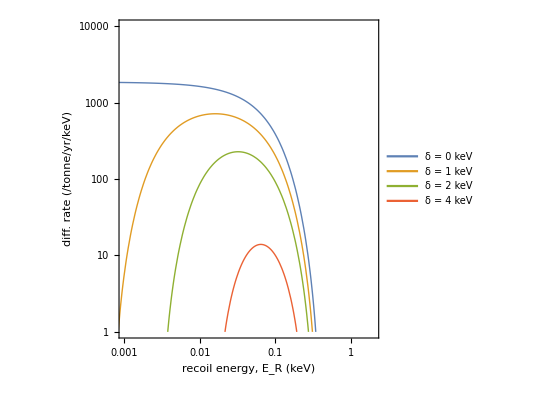

```mathematica
LogLogPlot[{dRdEr[ERkeV,0,0,10^-45,2,131],dRdEr[ERkeV,1,0,10^-45,2,131],dRdEr[ERkeV,2,0,10^-45,2,131],dRdEr[ERkeV,4,0,10^-45,2,131]},{ERkeV,10^-4,40},PlotLegends->Legend[{"δ = 0 keV","δ = 1 keV","δ = 2 keV","δ = 4 keV"}],FrameLabel->{"recoil energy, E_R (keV)","diff. rate (/tonne/yr/keV)"},PlotRange->{{10^-3,2},{1,10^4}},FrameTicks->{LogTicks[1,10^6],LogTicks[10^-6,1]}]
```

Exothermic:

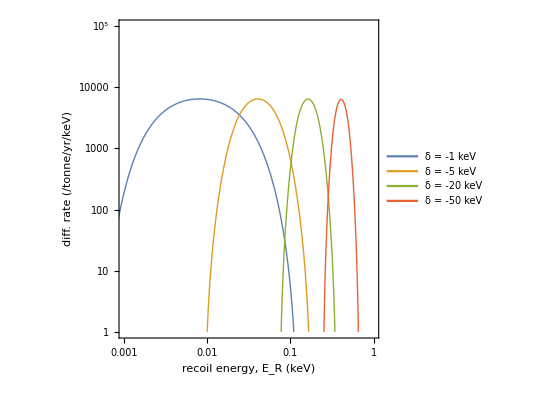

```mathematica
LogLogPlot[{dRdEr[ER,-1,0,10^-45,1,131],dRdEr[ER,-5,0,10^-45,1,131],dRdEr[ER,-20,0,10^-45,1,131],dRdEr[ER,-50,0,10^-45,1,131]},{ER,10^-4,40},PlotLegends->Legend[{"δ = -1 keV","δ = -5 keV","δ = -20 keV","δ = -50 keV"},LegendLayout->{"Column",2},Position->{.6,.9}],FrameLabel->{"recoil energy, E_R (keV)","diff. rate (/tonne/yr/keV)"},PlotRange->{{10^-3,1},{10^0,  10^5}},
FrameTicks->{LogTicks[10^-6,10^6],LogTicks[10^-6,20]}]
```

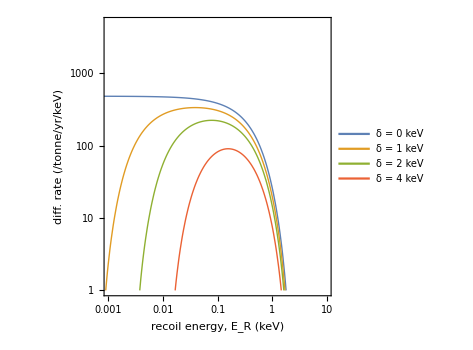
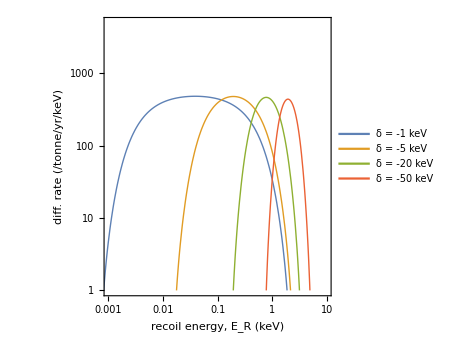

```mathematica
With[{mx=5,σ=10^-45},
{LogLogPlot[{dRdEr[ERkeV,0,0,σ,mx,131],dRdEr[ERkeV,1,0,σ,mx,131],dRdEr[ERkeV,2,0,σ,mx,131],dRdEr[ERkeV,4,0,σ,mx,131]},{ERkeV,10^-4,40},PlotLegends->Legend[{"δ = 0 keV","δ = 1 keV","δ = 2 keV","δ = 4 keV"}],FrameLabel->{"recoil energy, E_R (keV)","diff. rate (/tonne/yr/keV)"},
PlotRange->{{10^-3,10},{1,5 10^3}},FrameTicks->{LogTicks[1,10^6],LogTicks[10^-6,10]},ImageSize->350],
LogLogPlot[{dRdEr[ER,-1,0,σ,mx,131],dRdEr[ER,-5,0,σ,mx,131],dRdEr[ER,-20,0,σ,mx,131],dRdEr[ER,-50,0,σ,mx,131]},{ER,10^-4,40},PlotLegends->Legend[{"δ = -1 keV","δ = -5 keV","δ = -20 keV","δ = -50 keV"},LegendLayout->{"Column",2},Position->{.6,.9}],FrameLabel->{"recoil energy, E_R (keV)","diff. rate (/tonne/yr/keV)"},
PlotRange->{{10^-3,10},{10^0,  5 10^3}},ImageSize->350,GridLines->{None,{500}},
FrameTicks->{LogTicks[10^-6,10^6],LogTicks[10^-6,20]}]}
]
```

## Migdal rate

### Import

```mathematica
NotebookDirectory[]//SetDirectory;
datXe=Import["data/Xe_new.dat"];
datSepXe=Table[datXe[[4+254j;;254+254j]],{j,0,Floor[Length[datXe]/256]}];
```

#### Reproducing Fig.3

Xenon

```mathematica
datN1=Table[datXe[[4+254j;;254+254j]],{j,0,0}];
datN2=Table[datXe[[4+254j;;254+254j]],{j,1,2}];
datN3=Table[datXe[[4+254j;;254+254j]],{j,3,5}];
datN4=Table[datXe[[4+254j;;254+254j]],{j,6,8}];
datN5=Table[datXe[[4+254j;;254+254j]],{j,9,10}];
```

```mathematica
Me=511keV;
```

```mathematica
totN1={datN1[[1,All,1]]/1000,1000/(2π)((10^-3 Me)/(.001keV))^2 datN1[[All,All,2]][[1]]}//Thread;
totN2={datN2[[1,All,1]]/1000,1000/(2π)((10^-3 Me)/(.001keV))^2 Apply[Plus,datN2[[All,All,2]]]}//Thread;
totN3={datN3[[1,All,1]]/1000,1000/(2π)((10^-3 Me)/(.001keV))^2 Apply[Plus,datN3[[All,All,2]]]}//Thread;
totN4={datN4[[1,All,1]]/1000,1000/(2π)((10^-3 Me)/(.001keV))^2 Apply[Plus,datN4[[All,All,2]]]}//Thread;
totN5={datN5[[1,All,1]]/1000,1000/(2π)((10^-3 Me)/(.001keV))^2 Apply[Plus,datN5[[All,All,2]]]}//Thread;
```

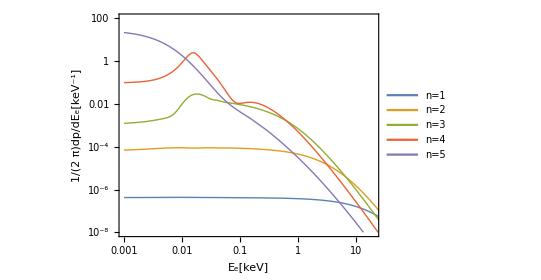

```mathematica
plot=ListLogLogPlot[{totN1,totN2,totN3,totN4,totN5},Joined->True,AspectRatio->.7,PlotRange->{{.001,20},{10^-8,100}},PlotLegends->Legend[{"n=1","n=2","n=3","n=4","n=5"}],FrameLabel->{"E_e[keV]","1/(2  π)dp/dE_e[keV^-1]"},FrameTicks->{LogTicks[10^-8,100,2],LogTicks[.001,10]}]
```

### Migdal Definitions

Nuclear recoil queching factor:

```mathematica
LeffXe=0.15;
```

Momentum transfer to electron:

```mathematica
qeKeV[ErGeV_,MtGeV_]=Me/keV √((2ErGeV)/MtGeV);
```

List of states contained in the file

```mathematica
statesXe=Table[datXe[[2+254j]],{j,0,Floor[Length[datXe]/256]}];
```

List of binding energies of the states in keV

```mathematica
EstatesXe=1/1000{3.5 10^4,5.4 10^3,4.9 10^3,1.1 10^3,9.3 10^2,6.6 10^2,2.0 10^2,1.4 10^2,6.1 10,2.1 10,9.8};
```

Array of binding energies, can be accessed as Enl[[n,l]]

```mathematica
EnlXe=1/1000{{3.5 10^4,0,0,0},{5.4 10^3,4.9 10^3,0,0},{1.1 10^3,9.3 10^3,6.6 10^2,0},{2.0 10^2,1.4 10^2,6.1 10,0.85},{2.1 10,9.8,1.6,0},{3.3,2.2,0,0}};
```

Ionization probability for the (n,l) state into a free state with kinetic energy E_e from momentum kick q_e

```mathematica
z[x_]=0;
```

```mathematica
znlxeTable=Table[If[EnlXe[[ni,li+1]]>0,(Switch@@Join[{{ni,li}},({statesXe,Table[datSepXe[[i]]//Interpolation,{i,1,datSepXe//Length}]}//Thread//Flatten[#,1]&)]),z],{ni,1,Length[EnlXe]},{li,0,3}];
```

Setting probability to zero below threshold doesn’t seem to have an affect on limits, but doesn’t match rates in Ibe et al.:

```mathematica
ZnlXe[n_,l_,qEkeV_,Ee_ ]:=If[(1000Ee)>1,(qEkeV/(.001))^2 1000/(2π)znlxeTable⟦n,l+1⟧[1000Ee],0]
```

```mathematica
ZnlXe[n_,l_,qEkeV_,Ee_ ]:=If[(1000Ee)>1,(qEkeV/(.001))^2 1000/(2π)znlxeTable⟦n,l+1⟧[1000Ee],(qEkeV/(.001))^2 1000/(2π)znlxeTable⟦n,l+1⟧[.001]];
```

### Differential rate definition

The differential Migdal rate for a given atomic shell (constant quenching factor):

```mathematica
dRmigdEdet//Clear;
```

```mathematica
dRmigdEdet[EdetkeV_?NumericQ,δDMkeV_?NumericQ,σ_?NumericQ,Mx_?NumericQ,Ni_?IntegerQ,ERthGeV_:MinERcutoffGeV] :=
If[EdetkeV<Min[EstatesXe[[Position[statesXe[[All,1]],Ni]//Flatten]]]||EdetkeV>(EdetMax[δDMkeV 10^-6,Mx,131 amu/GeV] 10^6),0,
NIntegrate[
dRdEr[ErkeV,δDMkeV,(EdetkeV-ErkeV*LeffXe),σ,Mx,131]*
 Sum[
UnitStep[(EdetkeV-ErkeV*LeffXe)-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qeKeV[ErkeV 10^-6,131 amu/GeV ],EdetkeV-ErkeV*LeffXe-EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{ErkeV,
Max[ErMinGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131. amu/GeV] 10^6,ERthGeV 10^6],
Min[(EdetkeV-Min[EstatesXe[[Position[statesXe[[All,1]],Ni]//Flatten]]])/(.15),ErMaxGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131 amu/GeV] 10^6]},PrecisionGoal->3]]
```

### Elastic Migdal rate

```mathematica
dataNR=ParallelTable[{Edet,1/LeffXe dRdEr[Edet /LeffXe,0,0,10^-40,2,131]},{Edet,logSpace[.001,LeffXe 10^6 ErMax[VMAX,0,0,2,131 amu/GeV],200]}];
dataEM3=ParallelTable[{Edet,dRmigdEdet[Edet,0,10^-40,2,3]},{Edet,logSpace[.66,3,100]}];
dataEM4=ParallelTable[{Edet,dRmigdEdet[Edet,0,10^-40,2,4]},{Edet,logSpace[.06,3,100]}];
dataEM5=ParallelTable[{Edet,dRmigdEdet[Edet,0,10^-40,2,5]},{Edet,logSpace[.01,2,100]}];
```

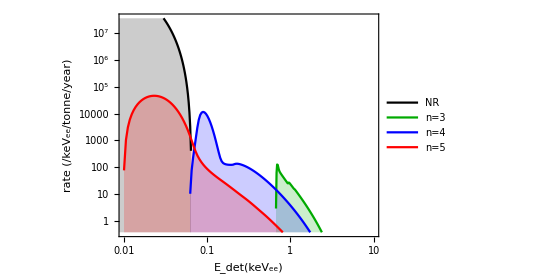

```mathematica
ListLogLogPlot[{dataNR,dataEM3,dataEM4,dataEM5},Joined->True,PlotRange->{{.01,10},{365250 10^-6,365250 10^2}},
FrameTicks->{LogTicks[10^-7,10^10,2],LogTicks[10^-2,10^1,1]},
PlotStyle->{Black,Green//Darker,Blue,Red},
FrameLabel->{"E_det(keV_ee)","rate (/keV_ee/tonne/year)"},
PlotLegends->Legend[{"NR","n=3","n=4","n=5"}],AspectRatio->.7,Filling->Bottom]
```

This matches Fig.5 of Ibe et al.

### Compare Lindhard to constant L

With Lindhard factor from 1412.4417:

```mathematica
k=0.1394;
g[ϵ_]:=3 ϵ^0.15+0.7 ϵ^0.6+ϵ;
LindXe[ErkeV_]=(k g[11.5 ErkeV 54^(-7/5)])/(1+k g[11.5 ErkeV 54^(-7/5)])
```

(0.1394 (1.87251 ErkeV^0.15+0.106244 ErkeV^0.6+0.0431864 ErkeV))/(1+0.1394 (1.87251 ErkeV^0.15+0.106244 ErkeV^0.6+0.0431864 ErkeV))

```mathematica
LindXeF=Table[{er,LindXe[er]},{er,0,1,.001}]//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
dRmigLdEdet[EdetkeV_?NumericQ,δDMkeV_?NumericQ,σ_?NumericQ,Mx_?NumericQ,Ni_,ERthGeV_:MinERcutoffGeV] :=NIntegrate[
dRdEr[ErkeV,δDMkeV,(EdetkeV-ErkeV*LindXeF[ErkeV]),σ,Mx,131]*
 Sum[
UnitStep[(EdetkeV-ErkeV*LindXeF[ErkeV])-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qeKeV[ErkeV 10^-6,131 amu/GeV ],EdetkeV-ErkeV*LindXeF[ErkeV]-EstatesXe[[nl]]],
{nl,Position[statesXe[[All,1]],Ni]//Flatten}],
{ErkeV,ErMinGeV[(δDMkeV) 10^-6,0,Mx,131. amu/GeV] 10^6,ErMaxGeV[(δDMkeV) 10^-6,0,Mx,131. amu/GeV] 10^6},PrecisionGoal->3]
```

```mathematica
dataNRL=ParallelTable[{ER LindXeF[ER],1/LindXeF[ER] dRdEr[ER,0,0,10^-40,2,131]},{ER,logSpace[.05,10^6 ErMax[VMAX,0,0,2,131 amu/GeV],1000]}];
dataEML3=ParallelTable[{Edet,dRmigLdEdet[Edet,0,10^-40,2,3]},{Edet,logSpace[.66,3,100]}];
dataEML4=ParallelTable[{Edet,dRmigLdEdet[Edet,0,10^-40,2,4]},{Edet,logSpace[.06,3,100]}];
dataEML5=ParallelTable[{Edet,dRmigLdEdet[Edet,0,10^-40,2,5]},{Edet,logSpace[.01,2,100]}];
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Compare Lindhard to constant L

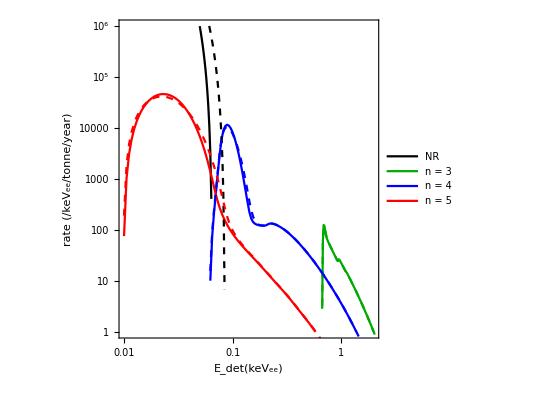

```mathematica
migPlotN=Show[ListLogLogPlot[{dataNR,dataEM3,dataEM4,dataEM5},Joined->True,PlotRange->{{.009999,2},{10^0,10^6}},
FrameTicks->{LogTicks[10^-7,10^10,2],LogTicks[10^-2,10^1,1]},
PlotStyle->{Black,Green//Darker,Blue,Red},
FrameLabel->{"E_det(keV_ee)","rate (/keV_ee/tonne/year)"},
PlotLegends->Legend[{"NR","n = 3","n = 4","n = 5"}]],ListLogLogPlot[{dataNRL,dataEML3,dataEML4,dataEML5},Joined->True,
PlotStyle->{{Black,Dashed},{Dashed,Green//Darker},{Dashed,Blue},{Dashed,Red}}]]
```

```mathematica
Export["figures/fig_migRate_lindhard.pdf",migPlotN];
```

#### Total rate comparison

```mathematica
rateEM3=dataEM3//Interpolation;
rateEM4=dataEM4//Interpolation;
rateEM5=dataEM5//Interpolation;
rateEML3=dataEML3//Interpolation;
rateEML4=dataEML4//Interpolation;
rateEML5=dataEML5//Interpolation;
```

```mathematica
constLrate=NIntegrate[rateEM3[er],{er,dataEM3[[1,1]],dataEM3[[-1,1]]}]+NIntegrate[rateEM4[er],{er,dataEM4[[1,1]],dataEM4[[-1,1]]}]+NIntegrate[rateEM5[er],{er,dataEM5[[1,1]],dataEM5[[-1,1]]}]
```

1537.59

```mathematica
lindLrate=NIntegrate[rateEML3[er],{er,dataEML3[[1,1]],dataEML3[[-1,1]]}]+NIntegrate[rateEML4[er],{er,dataEML4[[1,1]],dataEML4[[-1,1]]}]+NIntegrate[rateEML5[er],{er,dataEML5[[1,1]],dataEML5[[-1,1]]}]
```

1537.65

```mathematica
constLrate/lindLrate
```

0.999962

## Best fit rates

### Define integrated rate

```mathematica
Xe1tMigRate[eMin_?NumericQ,eMax_?NumericQ,σ_?NumericQ,Mx_?NumericQ,δDMkeV_?NumericQ,ERthGeV_:MinERcutoffGeV]:=
If[eMin>EdetMax[δDMkeV 10^-6,Mx,131 amu/GeV] 10^6,0,
NIntegrate[
dRdEr[ErkeV,δDMkeV,(EdetkeV-ErkeV*LeffXe),σ,Mx,131]*
 Sum[
UnitStep[(EdetkeV-ErkeV*LeffXe)-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qeKeV[ErkeV 10^-6,131 amu/GeV ],EdetkeV-ErkeV*LeffXe-EstatesXe[[nl]]],
{nl,Range[4,11]}],
{EdetkeV,eMin,eMax},
{ErkeV,
Max[ErMinGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131. amu/GeV] 10^6,ERthGeV 10^6],
Max[ErMaxGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131. amu/GeV] 10^6,ERthGeV 10^6]},PrecisionGoal->3]]
```

#### Calculate elastic rates

```mathematica
migTotM2δ0=ParallelTable[{Edet,dRmigdEdet[Edet,0,10^-40,2,5]+dRmigdEdet[Edet,0,10^-40,2,4]+dRmigdEdet[Edet,0,10^-40,2,3]},{Edet,logSpace[.01,3,100]}];
```

```mathematica
migTotMp5δ0=ParallelTable[{Edet,dRmigdEdet[Edet,0,10^-40,0.5,5]+dRmigdEdet[Edet,0,10^-40,0.5,4]+dRmigdEdet[Edet,0,10^-40,0.5,3]},{Edet,logSpace[.01,3,100]}];
```

Calculate integrated rate for fits:

```mathematica
nBins=5;
```

```mathematica
binB2=logSpace[.186,2,nBins+1];
elasMigRateM2=Table[Xe1tMigRate[binB2[[ii]],binB2[[ii+1]],10^-40,2,0],{ii,1,nBins}];
```

```mathematica
binBp5=logSpace[.186,1.5,nBins+1];
elasMigRateMp5=Table[Xe1tMigRate[binBp5[[ii]],binBp5[[ii+1]],10^-40,0.5,0],{ii,1,nBins}];
```

### Combined plots

#### m_χ=2GeV

```mathematica
BestFitM2=
{{NMinimize[{dataEMin=Table[Xe1tMigRate[binB2[[ii]],binB2[[ii+1]],10^-40,mass,-4],{ii,1,nBins}];
Plus@@((elasMigRateM2-σ dataEMin)^2/elasMigRateM2),σ>0,0.4<mass<2},{σ,mass},PrecisionGoal->2],δDM->-4}//Flatten
,{NMinimize[{dataEMin=Table[Xe1tMigRate[binB2[[ii]],binB2[[ii+1]],10^-40,mass,4],{ii,1,nBins}];
Plus@@((elasMigRateM2-σ dataEMin)^2/elasMigRateM2),σ>0,0.4<mass<2},{σ,mass},PrecisionGoal->2],δDM->4}//Flatten};
```

Un-comment to use pre-calculated values:

```mathematica
(*BestFitM2={{0.8718096784364927,σ->0.6803322377489064,mass->0.4582381004697444,δDM->-4},{0.3174743804851736,σ->3.4978366680522615,mass->3.057260120368556,δDM->4}};*)
```

```mathematica
migTotBFexoM2δ4=ParallelTable[{Edet,dRmigdEdet[Edet,δDM,σ 10^-40,mass,5]+dRmigdEdet[Edet,δDM,σ 10^-40,mass,4]+dRmigdEdet[Edet,δDM,σ 10^-40,mass,3]}/.BestFitM2[[1,2;;All]],{Edet,logSpace[.01,2.2,50]}];
migTotBFendoM2δ4=ParallelTable[{Edet,dRmigdEdet[Edet,δDM,σ 10^-40,mass,5]+dRmigdEdet[Edet,δDM,σ 10^-40,mass,4]+dRmigdEdet[Edet,δDM,σ 10^-40,mass,3]}/.BestFitM2[[2,2;;All]],{Edet,logSpace[.01,2,50]}];
```

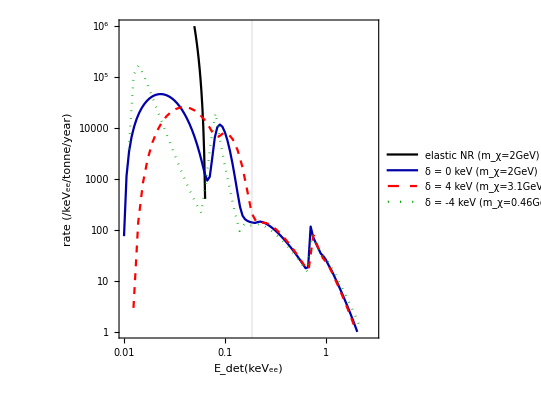

```mathematica
migPlotBFm2=ListLogLogPlot[{dataNR,migTotM2δ0,migTotBFendoM2δ4,migTotBFexoM2δ4},Joined->True,PlotRange->{{.01,3},{10^0,10^6}},
FrameTicks->{LogTicks[10^-7,10^10,2],LogTicks[10^-2,10^1,1]},
PlotStyle->{Black,Blue//Darker,{Red,Dashed},{Green//Darker,Dotted}},
FrameLabel->{"E_det(keV_ee)","rate (/keV_ee/tonne/year)"},
GridLines->{{.186},{}},
PlotLegends->Legend[{"elastic NR (m_χ=2GeV)","δ = 0 keV (m_χ=2GeV)","δ = 4 keV (m_χ=3.1GeV)","δ = -4 keV (m_χ=0.46GeV) "},Position->{.7,.84}]]
```

#### m_χ=0.5GeV

```mathematica
BestFitMp5=
{{NMinimize[{dataEMin=ParallelTable[Xe1tMigRate[binBp5[[ii]],binBp5[[ii+1]],10^-40,mass,-4],{ii,1,nBins}];
Plus@@((elasMigRateMp5-σ dataEMin)^2/elasMigRateMp5),.1>σ>0,0.001<mass<.5},{σ,mass},PrecisionGoal->2],δ->-4}//Flatten,{NMinimize[{dataEMin=ParallelTable[Xe1tMigRate[binBp5[[ii]],binBp5[[ii+1]],10^-40,mass,4],{ii,1,nBins}];
Plus@@((elasMigRateMp5-σ dataEMin)^2/elasMigRateMp5),σ>0,0.5<mass<2},{σ,mass},PrecisionGoal->2],δ->4}//Flatten};
```

Un-comment to use pre-calculated values:

```mathematica
(*BestFitMp5={{0.08863532307502638,σ->0.003699672607425221,mass->0.00181,δ->-4},{0.0007578776792402522,σ->27.36059009062346,mass->1.6363565810444212,δ->4}};*)
```

```mathematica
migTotBFexoMp5δ4=ParallelTable[{Edet,dRmigdEdet[Edet,δ,σ 10^-40,mass,5]+dRmigdEdet[Edet,δ,σ 10^-40,mass,4]+dRmigdEdet[Edet,δ,σ 10^-40,mass,3]}/.BestFitMp5[[1,2;;All]],{Edet,logSpace[.0115,2,100]}];
migTotBFendoMp5δ4=ParallelTable[{Edet,dRmigdEdet[Edet,δ,σ 10^-40,mass,5]+dRmigdEdet[Edet,δ,σ 10^-40,mass,4]+dRmigdEdet[Edet,δ,σ 10^-40,mass,3]}/.BestFitMp5[[2,2;;All]],{Edet,logSpace[.0115,2,100]}];
```

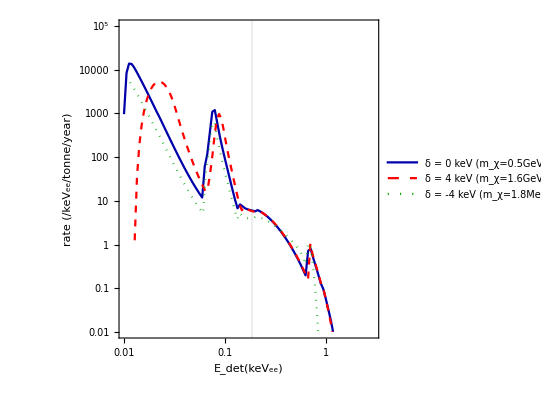

```mathematica
migPlotBFmp5=ListLogLogPlot[{migTotMp5δ0,migTotBFendoMp5δ4,migTotBFexoMp5δ4},Joined->True,PlotRange->{{.01,3},{10^-2,10^5}},
FrameTicks->{LogTicks[10^-7,10^10,2],LogTicks[10^-2,10^1,1]},
PlotStyle->{Blue//Darker,{Red,Dashed},{Green//Darker,Dotted}},
FrameLabel->{"E_det(keV_ee)","rate (/keV_ee/tonne/year)"},

GridLines->{{.186},{}},
PlotLegends->Legend[{"δ = 0 keV (m_χ=0.5GeV)","δ = 4 keV (m_χ=1.6GeV)","δ = -4 keV (m_χ=1.8MeV) "},Position->{0.7,.85}]]
```

```mathematica
Export["./fig_migRate_M2.pdf",migPlotBFm2];
Export["./fig_migRate_Mp5.pdf",migPlotBFmp5];
```

## Experimental constraints

### Nuclear recoil limits

#### S2-only analysis statistics

Import data

```mathematica
NotebookDirectory[]//SetDirectory;
s2datRaw=Import["data/s2_only_data.csv"]//Drop[#,1]&;
s2bgExp=Import["data/s2_only_expected.csv"]//Drop[#,1]&;
s2datBins=Import["data/xe1t_s2only_bins.csv"];
s2erCalib=Import["data/xe1t_s2only_s2er_calib.csv"]//Interpolation[{#[[All,2]],#[[All,1]]}//Thread,InterpolationOrder->1]&;
s2nrXe1tLim=Import["data/xe1t_SInr_S2only_2019.csv"];
```

Effective exposure in tonne-years

```mathematica
xe1tEffectiveExpNRS2=Import["data/xe1t_effExp_s2only_NR.csv"]//{#[[All,1]],#[[All,2]]/365.25}&//Thread//Prepend[#,{.7,0}]&//Prepend[#,{0,0}]&//Interpolation[#,InterpolationOrder->1]&;
```

Convert s2 data to absolute number of events:

```mathematica
bins=logSpace[150,3000,Length[s2datRaw]+1]
```

{150.,192.535,247.132,317.211,407.163,522.621,670.82,861.044,1105.21,1418.61,1820.89,2337.23,3000.}

```mathematica
binsWidthsER=Table[s2erCalib[bins[[i+1]]]-s2erCalib[bins[[i]]],{i,1,Length[bins]-1}]
```

InterpolatingFunction::dmval: Input value {3000.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{0.0336994,0.0442624,0.0596508,0.0727782,0.083159,0.112834,0.132808,0.190923,0.328027,0.489881,0.720956,1.36878}

Data reported per tonne.day.keV_ee, convert this to total number of events in the 22 tonne.day exposure:

```mathematica
s2dat=22s2datRaw[[All,2]]binsWidthsER;
s2exp=22s2bgExp[[All,2]]binsWidthsER;
```

Total expected events:

```mathematica
Nexp=Plus@@s2exp
```

23.3908

Total observed:

```mathematica
Nobs=Plus@@s2dat
```

60.852

Find CL90%

```mathematica
logpERs2[x_,bgexp_,obs_,bgN_]=-(bgexp bgN+x)+obs Log[bgexp bgN+x]-Log[obs!]+Log[PDF[NormalDistribution[1,.15],bgN]];
```

```mathematica
sol=FindMinimum[{(√(-2(logpERs2[x,Nexp,Nobs,1]-logpERs2[Nobs-Nexp,Nexp,Nobs,1]))-InverseCDF[NormalDistribution[0,1],0.90])^2,x>1},{x,40}]
```

{7.02364×10^-17,{x→48.0131}}

Or including uncertainty in background:

bgNorm which maximizes the likelihood for a given x:

```mathematica
bgNcondMax[x_,bgexp_,obs_]=bgN/.(Solve[D[-(bgexp bgN+x)+obs Log[bgexp bgN+x]-Log[obs!]+Log[PDF[NormalDistribution[1,.15],bgN]],bgN]==0,bgN][[2,1]]);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
logpERs2[x_?NumericQ,bgexp_,obs_]=-(bgexp bgNcondMax[x,bgexp,obs]+x)+obs Log[bgexp bgNcondMax[x,bgexp,obs]+x]-Log[obs!]+Log[PDF[NormalDistribution[1,.15],bgNcondMax[x,bgexp,obs]]];
```

```mathematica
sol=FindMinimum[{(√(-2(logpERs2[x,Nexp,Nobs,bgNcondMax[x,Nexp,Nobs]]-logpERs2[Nobs-Nexp,Nexp,Nobs,1]))-InverseCDF[NormalDistribution[0,1],0.90])^2,x>1},{x,40}]
```

{7.77418×10^-17,{x→48.8913}}

```mathematica
NupperLimit=x/.sol[[2]]
```

48.8913

#### Define total event rates

```mathematica
NReventsXe1tS2only[δDMkeV_?NumericQ,σncm2_?NumericQ,mxGeV_?NumericQ]:=If[δMaxGeV[mxGeV,131 amu/GeV]<δDMkeV 10^-6,0,
(365.25 3600*24 s/(1(*year*)))(c(100000cm)/km)((1 GeV)/(10^6(*keV*)))(GeVperKg (1000kg)/(1(*tonne*)))*
(ρ/(2mxGeV GeV))(1/μ[mn,mxGeV GeV]^2)( σncm2 cm^2)NIntegrate[xe1tEffectiveExpNRS2[ErkeV](131^2 F[131,ErkeV]^2) Gv[Vmin[ErkeV 10^-6,δDMkeV 10^-6,0,mxGeV,131 amu/GeV]],{ErkeV,Max[.7,10^6 ErMinGeV[δDMkeV 10^-6,0,mxGeV,131 amu/GeV]],Min[40,10^6 ErMaxGeV[δDMkeV 10^-6,0,mxGeV,131 amu/GeV]]},PrecisionGoal->2,Method->{Automatic,"SymbolicProcessing"->False}]]
```

#### Calculate upper limits

```mathematica
xe1tS2datNRmxCSendo=ParallelTable[
{mx,NupperLimit /(NReventsXe1tS2only[δ,1,mx]+10^-100)},
{δ,{0,5,10,50,100,200}},
{mx,logSpace[1,10,200]}];
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

```mathematica
xe1tS2datNRmxCSexo=ParallelTable[
{mx,NupperLimit /(NReventsXe1tS2only[δ,1,mx]+10^-100)},
{δ,{0,-5,-10,-50}},
{mx,logSpace[1,10,200]}];
```

NIntegrate::izero: 
   Integral and error estimates are 0 on all integration subregions. Try
    increasing the value of the MinRecursion option. If value of integral may
    be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero
     will be suppressed during this calculation.

```mathematica
s2nrLim=ListLogLogPlot[{xe1tS2datNRmxCSexo[[3]],xe1tS2datNRmxCSendo[[1]],xe1tS2datNRmxCSendo[[3]]},Joined->True,
PlotRange->{{.001,10},{10^-45,10^-30}},FrameLabel->{"DM mass, m_χ (GeV)","inelastic cross section, σ_χp (cm^2)"},
FrameTicks->{LogTicks[10^-48,10^-33,2],LogTicks[10^0,10^4]}];
```

### Migdal limits

#### S2-only analysis

```mathematica
xe1tEffectiveExpERS2=Import["data/xe1t_effExp_s2only_ER.csv"]//{#[[All,1]],#[[All,2]]/365.25}&//Thread//Prepend[#,{.183,0}]&//Prepend[#,{0,0}]&//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
Xe1tMigRateS2[σ_?NumericQ,Mx_?NumericQ,δDMkeV_?NumericQ,ERthGeV_:MinERcutoffGeV] :=If[δMaxGeV[Mx,131 amu/GeV] 10^6<δDMkeV,0,
NIntegrate[xe1tEffectiveExpERS2[EdetkeV]UnitStep[EdetMax[δDMkeV 10^-6,Mx,131 amu/GeV] 10^6-EdetkeV]
dRdEr[ErkeV,δDMkeV,(EdetkeV-ErkeV*LeffXe),σ,Mx,131]*
 Sum[
UnitStep[(EdetkeV-ErkeV*LeffXe)-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qeKeV[ErkeV 10^-6,131. amu/GeV ],EdetkeV-ErkeV*LeffXe-EstatesXe[[nl]]],
{nl,{Position[statesXe[[All,1]],4],Position[statesXe[[All,1]],3],Position[statesXe[[All,1]],5]}//Flatten}],
{EdetkeV,0.189,3.827},
{ErkeV,Max[ErMinGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131. amu/GeV] 10^6,ERthGeV 10^6],Max[ErMaxGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131 amu/GeV] 10^6,ERthGeV 10^6]},PrecisionGoal->2]]
```

```mathematica
xe1tMigdalLimS2={ParallelTable[
{mx,NupperLimit /(Xe1tMigRateS2[1,mx,-10]+10^-100)},
{mx,logSpace[.00065,3,60]}],
ParallelTable[
{mx,NupperLimit /(Xe1tMigRateS2[1,mx,0]+10^-100)},
{mx,logSpace[.04,4,40]}],
ParallelTable[
{mx,NupperLimit /(Xe1tMigRateS2[1,mx,10]+10^-100)},
{mx,logSpace[1,6,20]}]};
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

```mathematica
MigLimitPlot=Show[ListLogLogPlot[{xe1tS2datNRmxCSexo[[3,1;;172]],xe1tS2datNRmxCSendo[[1,1;;181]],xe1tS2datNRmxCSendo[[2,1;;183]]},Joined->True,
PlotRange->{{.00061,8},{10^-43,10^-31}},
PlotStyle->{Green//Darker,Blue,Red//Darker},FrameLabel->{"DM mass, m_χ (GeV)","inelastic cross section, f_*σ_χp (cm^2)"},
FrameTicks->{LogTicks[10^-47,10^-30,2],LogTicks[10^-3,10^4]}],ListLogLogPlot[xe1tMigdalLimS2,Joined->True,PlotStyle->{{DotDashed,Green//Darker},{DotDashed,Blue},{DotDashed,Red//Darker}}]];
```

#### LZ projections

Define number of events for LZ assuming a threshold of 0.5 keV_ee and using Xe1t ER efficiency:

```mathematica
xe1tEff=Import["data/xenon1t_eff_excess.csv"]//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
LZMigEvents[σ_?NumericQ,Mx_?NumericQ,δDMkeV_?NumericQ,ERthGeV_:MinERcutoffGeV] :=If[δMaxGeV[Mx,131 amu/GeV] 10^6<δDMkeV,0,
(5.6 1000)/365.25 NIntegrate[xe1tEff[EdetkeV]UnitStep[EdetMax[δDMkeV 10^-6,Mx,131 amu/GeV] 10^6-EdetkeV]
dRdEr[ErkeV,δDMkeV,(EdetkeV-ErkeV*LeffXe),σ,Mx,131]*
 Sum[
UnitStep[(EdetkeV-ErkeV*LeffXe)-EstatesXe[[nl]]]*
ZnlXe[statesXe[[nl,1]],statesXe[[nl,2]],qeKeV[ErkeV 10^-6,131. amu/GeV ],EdetkeV-ErkeV*LeffXe-EstatesXe[[nl]]],
{nl,{Position[statesXe[[All,1]],4],Position[statesXe[[All,1]],3],Position[statesXe[[All,1]],5]}//Flatten}],
{EdetkeV,.5,4},
{ErkeV,Max[ErMinGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131. amu/GeV] 10^6,ERthGeV 10^6],Max[ErMaxGeV[(δDMkeV) 10^-6,EdetkeV 10^-6,Mx,131 amu/GeV] 10^6,ERthGeV 10^6]},PrecisionGoal->2]]
```

Dominant background in low-energy region is Rn222, at 2x 10^-5 dru

```mathematica
Nexp=Nobs=2 10^-5 5600 1000 3.5
```

392.

```mathematica
solLZ=FindMinimum[{(√(-2(logpERs2[x,Nexp,Nobs,bgNcondMax[x,Nexp,Nobs]]-logpERs2[Nobs-Nexp,Nexp,Nobs,1]))-InverseCDF[NormalDistribution[0,1],0.90])^2,x>1},{x,40}]
```

{1.23993×10^-15,{x→79.5689}}

```mathematica
NupperLimitLZ=x/.solLZ[[2]];
```

```mathematica
LZMigdalLim={ParallelTable[
{mx,NupperLimitLZ /(LZMigEvents[1,mx,-10]+10^-100)},
{mx,logSpace[.00065,3,50]}],
ParallelTable[
{mx,NupperLimitLZ /(LZMigEvents[1,mx,0]+10^-100)},
{mx,logSpace[.1,4,40]}],
ParallelTable[
{mx,NupperLimitLZ /(LZMigEvents[1,mx,10]+10^-100)},
{mx,logSpace[3,6,20]}]};
```

```mathematica
LZprojPlot=ListLogLogPlot[LZMigdalLim,Joined->True,PlotStyle->{{Thick,Dashing[Tiny],Green//Darker},{Dashing[Tiny],Blue},{Dashing[Tiny],Red//Darker}}];
```

#### Assemble final plot

```mathematica
table[pairs_]:=TableForm[{pairs[[1;;3,1]],pairs[[4;;6,1]],pairs[[7;;9,1]]},TableHeadings->Map[Style[#,12,FontFamily->"Times"]&,{{"Xe1t (NR)","Xe1t (Mig)","LZ (Mig)"},{"δ=-10","δ=0","δ=10"}},{2}],TableAlignments->Center,TableSpacing->{1,1}]
```

```mathematica
legend=ListLogLogPlot[{{0},{0},{0},{0},{0},{0},{0},{0},{0}},Joined->True,
PlotStyle->{{Green//Darker},{Blue},{Red//Darker},{DotDashed,Green//Darker},{DotDashed,Blue},{DotDashed,Red//Darker},{Dashing[Tiny],Green//Darker},{Dashing[Tiny],Blue},{Dashing[Tiny],Red//Darker}},
PlotLegends->Legend[{"","","","","","","","",""},LegendMargins->{{0,0},{0,0}},LegendMarkerSize->15,LegendFunction->(Framed[#,FrameMargins->0,Background->White]&),LegendLayout->table,Position->{.255,.88}]];
```

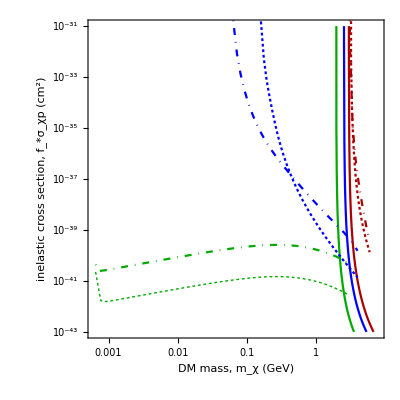

```mathematica
fullBoundPlot=Show[MigLimitPlot,LZprojPlot,legend]
```

```mathematica
Export["./fig_bounds.pdf",fullBoundPlot];
```

### Dark matter in excited state

Fixing αD based on relic abundance requirement for secluded DM (so mA<mχ):

```mathematica
{Tco,σχp}={(Ma^4 10^6 keV/GeV)/(αD^2 √Mχ √Td Mpl (10^-9 GeV)),(16 π ϵ^2 α αD μ[Mχ,mn]^2)/Ma^4(cm^2 Centimeter^-2)}/.αD->4 10^-5 Mχ/GeV(1-(Ma/Mχ)^2)/.{α->1/137,Mpl->10^19 GeV,Ma->.004 GeV,Mχ->.01GeV,Td->.0005GeV,ϵ->.3 10^-5}
```

{101.409 keV,1.6522×10^-40 cm^2}

```mathematica
f=(1+Exp[δ/Tco])^-1/.δ->10keV
```

0.475367

This can work across a range of masses:

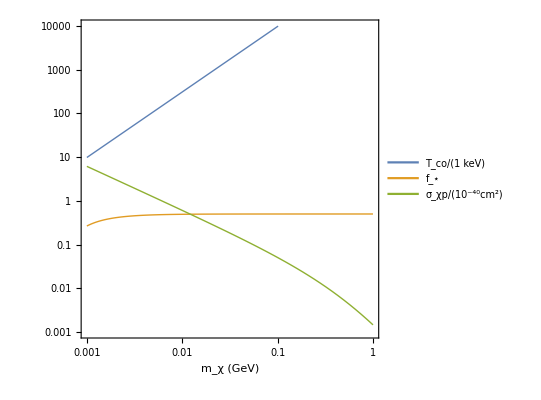

```mathematica
With[{δ=10,α=1/137,Mpl=10^19,Td=.0005,ϵ=.3 10^-5},
LogLogPlot[{((Mχ/2)^4 10^6 1)/((4 10^-5 Mχ(1-((Mχ/2)/Mχ)^2))^2 √Mχ √Td Mpl (10^-9)),(1+Exp[δ/(((Mχ/2)^4 10^6 1)/((4 10^-5 Mχ(1-((Mχ/2)/Mχ)^2))^2 √Mχ √Td Mpl (10^-9)))])^-1,(16 π ϵ^2 α (4 10^-5 Mχ(1-((Mχ/2)/Mχ)^2)) μ[Mχ,mn/GeV]^2)/(Mχ/2)^4(10^40 Centimeter^-2 GeV^-2)},{Mχ,.001,1},
FrameLabel->{"m_χ (GeV)",""},
PlotRange->{10^-3,10^4},FrameTicks->{LogTicks[10^-3,10^4],LogTicks[10^-3,10]},
PlotLegends->Legend[{"T_co/(1 keV)","f_⋆","σ_χp/(10^-40cm^2)"}]]]
```